```mathematica
(* Filename: Time_By_w1_SLE_tuck_A1_2A1_sym_DN
*)
(* Ver. 0 (28-Aug-2025) *)
(*
This file is used to prepare for a plot in Fig. 2.
*)
```

```mathematica
nn=127;
```

```mathematica
(***** In the following line, you need to set a path 
to the folder "For_figs_1_2". *****)
(*
datadir= "D:/.../For_figs_1_2/";
*)
```

```mathematica
mydirC4 = StringJoin[datadir,"/By_w1_SLE_tuck_A1_2A1_sym_DN/dt=1_4/Se16_Tr1000_B256"];
(***)
mydirC8 = StringJoin[datadir,"/By_w1_SLE_tuck_A1_2A1_sym_DN/dt=1_8/Se16_Tr1000_B256"];
(***)
mydirC16= StringJoin[datadir,"/By_w1_SLE_tuck_A1_2A1_sym_DN/dt=1_16/Se16_Tr1000_B256"];
(***)
mydirC32 = StringJoin[datadir,"/By_w1_SLE_tuck_A1_2A1_sym_DN/dt=1_32/Se16_Tr1000_B256"];
(***)
mydirC64 = StringJoin[datadir,"/By_w1_SLE_tuck_A1_2A1_sym_DN/dt=1_64/Se16_Tr1000_B256"];
(***)
mydirA14 = StringJoin[datadir,"/By_w2_revA_SRCK2_avr_Al_DN/dt=1_128/St14_Se16_Tr1000_B256"];
```

```mathematica
numSetForTime=16;
```

```mathematica
tmpfname=StringJoin["/Set_",ToString[1],"/timefile"];
tmpMiniList=Import[mydirC4<>tmpfname,"List"];
tmpMiniString=ToString[tmpMiniList];
tmpMiniString=StringReplace[tmpMiniString,"},}"->"}}}"];
locTmp=Flatten[ToExpression[tmpMiniString]];
timeListC4={locTmp};
For[iiset = 2,iiset≤numSetForTime,iiset++,
tmpfname=StringJoin["/Set_",ToString[iiset],"/timefile"];
tmpMiniList=Import[mydirC4<>tmpfname,"List"];
tmpMiniString=ToString[tmpMiniList];
tmpMiniString=StringReplace[tmpMiniString,"},}"->"}}}"];
locTmp=Flatten[ToExpression[tmpMiniString]];
timeListC4=Append[timeListC4,locTmp];
];
(***)
tmpfname=StringJoin["/Set_",ToString[1],"/timefile"];
tmpMiniList=Import[mydirC8<>tmpfname,"List"];
tmpMiniString=ToString[tmpMiniList];
tmpMiniString=StringReplace[tmpMiniString,"},}"->"}}}"];
locTmp=Flatten[ToExpression[tmpMiniString]];
timeListC8={locTmp};
For[iiset = 2,iiset≤numSetForTime,iiset++,
tmpfname=StringJoin["/Set_",ToString[iiset],"/timefile"];
tmpMiniList=Import[mydirC8<>tmpfname,"List"];
tmpMiniString=ToString[tmpMiniList];
tmpMiniString=StringReplace[tmpMiniString,"},}"->"}}}"];
locTmp=Flatten[ToExpression[tmpMiniString]];
timeListC8=Append[timeListC8,locTmp];
];
(***)
tmpfname=StringJoin["/Set_",ToString[1],"/timefile"];
tmpMiniList=Import[mydirC16<>tmpfname,"List"];
tmpMiniString=ToString[tmpMiniList];
tmpMiniString=StringReplace[tmpMiniString,"},}"->"}}}"];
locTmp=Flatten[ToExpression[tmpMiniString]];
timeListC16={locTmp};
For[iiset = 2,iiset≤numSetForTime,iiset++,
tmpfname=StringJoin["/Set_",ToString[iiset],"/timefile"];
tmpMiniList=Import[mydirC16<>tmpfname,"List"];
tmpMiniString=ToString[tmpMiniList];
tmpMiniString=StringReplace[tmpMiniString,"},}"->"}}}"];
locTmp=Flatten[ToExpression[tmpMiniString]];
timeListC16=Append[timeListC16,locTmp];
];
(***)
tmpfname=StringJoin["/Set_",ToString[1],"/timefile"];
tmpMiniList=Import[mydirC32<>tmpfname,"List"];
tmpMiniString=ToString[tmpMiniList];
tmpMiniString=StringReplace[tmpMiniString,"},}"->"}}}"];
locTmp=Flatten[ToExpression[tmpMiniString]];
timeListC32={locTmp};
For[iiset = 2,iiset≤numSetForTime,iiset++,
tmpfname=StringJoin["/Set_",ToString[iiset],"/timefile"];
tmpMiniList=Import[mydirC32<>tmpfname,"List"];
tmpMiniString=ToString[tmpMiniList];
tmpMiniString=StringReplace[tmpMiniString,"},}"->"}}}"];
locTmp=Flatten[ToExpression[tmpMiniString]];
timeListC32=Append[timeListC32,locTmp];
];
(***)
tmpfname=StringJoin["/Set_",ToString[1],"/timefile"];
tmpMiniList=Import[mydirC64<>tmpfname,"List"];
tmpMiniString=ToString[tmpMiniList];
tmpMiniString=StringReplace[tmpMiniString,"},}"->"}}}"];
locTmp=Flatten[ToExpression[tmpMiniString]];
timeListC64={locTmp};
For[iiset = 2,iiset≤numSetForTime,iiset++,
tmpfname=StringJoin["/Set_",ToString[iiset],"/timefile"];
tmpMiniList=Import[mydirC64<>tmpfname,"List"];
tmpMiniString=ToString[tmpMiniList];
tmpMiniString=StringReplace[tmpMiniString,"},}"->"}}}"];
locTmp=Flatten[ToExpression[tmpMiniString]];
timeListC64=Append[timeListC64,locTmp];
];
```

```mathematica
numSubSetForTime=8;(* 1, 2, 4, 8, 16 *)
numMiniSet=numSetForTime/numSubSetForTime;
```

```mathematica
timeListC4SubSum=Table[{},{iiset,1,numSubSetForTime}];
tmpSt=1;
tmpEnd=tmpSt-1+numMiniSet;
For[ll=1,ll<=numSubSetForTime,ll++,
timeListC4SubSum[[ll]]=timeListC4[[tmpSt,2]];
For[iiset=tmpSt+1,iiset<=tmpEnd,iiset++,
timeListC4SubSum[[ll]]+=timeListC4[[iiset,2]];
];
tmpSt+=numMiniSet;
tmpEnd=tmpSt-1+numMiniSet;
];
(***)
timeListC8SubSum=Table[{},{iiset,1,numSubSetForTime}];
tmpSt=1;
tmpEnd=tmpSt-1+numMiniSet;
For[ll=1,ll<=numSubSetForTime,ll++,
timeListC8SubSum[[ll]]=timeListC8[[tmpSt,2]];
For[iiset=tmpSt+1,iiset<=tmpEnd,iiset++,
timeListC8SubSum[[ll]]+=timeListC8[[iiset,2]];
];
tmpSt+=numMiniSet;
tmpEnd=tmpSt-1+numMiniSet;
];
(***)
timeListC16SubSum=Table[{},{iiset,1,numSubSetForTime}];
tmpSt=1;
tmpEnd=tmpSt-1+numMiniSet;
For[ll=1,ll<=numSubSetForTime,ll++,
timeListC16SubSum[[ll]]=timeListC16[[tmpSt,2]];
For[iiset=tmpSt+1,iiset<=tmpEnd,iiset++,
timeListC16SubSum[[ll]]+=timeListC16[[iiset,2]];
];
tmpSt+=numMiniSet;
tmpEnd=tmpSt-1+numMiniSet;
];
(***)
timeListC32SubSum=Table[{},{iiset,1,numSubSetForTime}];
tmpSt=1;
tmpEnd=tmpSt-1+numMiniSet;
For[ll=1,ll<=numSubSetForTime,ll++,
timeListC32SubSum[[ll]]=timeListC32[[tmpSt,2]];
For[iiset=tmpSt+1,iiset<=tmpEnd,iiset++,
timeListC32SubSum[[ll]]+=timeListC32[[iiset,2]];
];
tmpSt+=numMiniSet;
tmpEnd=tmpSt-1+numMiniSet;
];
(***)
timeListC64SubSum=Table[{},{iiset,1,numSubSetForTime}];
tmpSt=1;
tmpEnd=tmpSt-1+numMiniSet;
For[ll=1,ll<=numSubSetForTime,ll++,
timeListC64SubSum[[ll]]=timeListC64[[tmpSt,2]];
For[iiset=tmpSt+1,iiset<=tmpEnd,iiset++,
timeListC64SubSum[[ll]]+=timeListC64[[iiset,2]];
];
tmpSt+=numMiniSet;
tmpEnd=tmpSt-1+numMiniSet;
];
```

```mathematica
timeC4Ave=Mean[timeListC4SubSum];
timeC4Std=Sqrt[Total[(timeListC4SubSum-timeC4Ave)^2]/numSubSetForTime];
(***)
timeC8Ave=Mean[timeListC8SubSum];
timeC8Std=Sqrt[Total[(timeListC8SubSum-timeC8Ave)^2]/numSubSetForTime];
(***)
timeC16Ave=Mean[timeListC16SubSum];
timeC16Std=Sqrt[Total[(timeListC16SubSum-timeC16Ave)^2]/numSubSetForTime];
(***)
timeC32Ave=Mean[timeListC32SubSum];
timeC32Std=Sqrt[Total[(timeListC32SubSum-timeC32Ave)^2]/numSubSetForTime];
(***)
timeC64Ave=Mean[timeListC64SubSum];
timeC64Std=Sqrt[Total[(timeListC64SubSum-timeC64Ave)^2]/numSubSetForTime];
```

```mathematica
tmpMini=Table[{},{ii,1,5}];
tmpMini[[1]]={Log[2,timeC4Ave],Log[2,1/4]};
tmpMini[[2]]={Log[2,timeC8Ave],Log[2,1/8]};
tmpMini[[3]]={Log[2,timeC16Ave],Log[2,1/16]};
tmpMini[[4]]={Log[2,timeC32Ave],Log[2,1/32]};
tmpMini[[5]]={Log[2,timeC64Ave],Log[2,1/64]};
listTimeCForAve=Table[tmpMini[[ii]],{ii,1,5}];
```

```mathematica
plotlistTimeCForAve=ListPlot[listTimeCForAve];
```

```mathematica
tmpStep=1/4;
plotMiniBarC4ForTime=ListPlot[{{Log[2,timeC4Ave+timeC4Std],Log[2,tmpStep]},{Log[2,timeC4Ave-timeC4Std],Log[2,tmpStep]}},Joined->True,PlotStyle->Directive[GrayLevel[0.5],AbsoluteThickness[1.5],Opacity[0.66]]];
tmpStep/=2;
plotMiniBarC8ForTime=ListPlot[{{Log[2,timeC8Ave+timeC8Std],Log[2,tmpStep]},{Log[2,timeC8Ave-timeC8Std],Log[2,tmpStep]}},Joined->True,PlotStyle->Directive[GrayLevel[0.5],AbsoluteThickness[1.5],Opacity[0.66]]];
tmpStep/=2;
plotMiniBarC16ForTime=ListPlot[{{Log[2,timeC16Ave+timeC16Std],Log[2,tmpStep]},{Log[2,timeC16Ave-timeC16Std],Log[2,tmpStep]}},Joined->True,PlotStyle->Directive[GrayLevel[0.5],AbsoluteThickness[1.5],Opacity[0.66]]];
tmpStep/=2;
plotMiniBarC32ForTime=ListPlot[{{Log[2,timeC32Ave+timeC32Std],Log[2,tmpStep]},{Log[2,timeC32Ave-timeC32Std],Log[2,tmpStep]}},Joined->True,PlotStyle->Directive[GrayLevel[0.5],AbsoluteThickness[1.5],Opacity[0.66]]];
tmpStep/=2;
plotMiniBarC64ForTime=ListPlot[{{Log[2,timeC64Ave+timeC64Std],Log[2,tmpStep]},{Log[2,timeC64Ave-timeC64Std],Log[2,tmpStep]}},Joined->True,PlotStyle->Directive[GrayLevel[0.5],AbsoluteThickness[1.5],Opacity[0.66]]];
```

```mathematica
tmpUpperListC={{Log[2,timeC4Ave+timeC4Std],Log[2,1/4]},{Log[2,timeC8Ave+timeC8Std],Log[2,1/8]},{Log[2,timeC16Ave+timeC16Std],Log[2,1/16]},{Log[2,timeC32Ave+timeC32Std],Log[2,1/32]},{Log[2,timeC64Ave+timeC64Std],Log[2,1/64]}};
tmpLowerListC={{Log[2,timeC4Ave-timeC4Std],Log[2,1/4]},{Log[2,timeC8Ave-timeC8Std],Log[2,1/8]},{Log[2,timeC16Ave-timeC16Std],Log[2,1/16]},{Log[2,timeC32Ave-timeC32Std],Log[2,1/32]},{Log[2,timeC64Ave-timeC64Std],Log[2,1/64]}};
```

```mathematica
tmpLine=Line[{{0.,0.},{0,0.5}}];
tmpSize=5.0; (* 5.0, 10.0 *)
Graphics[{Gray(*RGBColor[0,0,1]*),tmpLine},AspectRatio->NCache[GoldenRatio^(-1),0.6180339887498948],Axes->None,AxesOrigin->{0,0},ImageSize->{tmpSize,Automatic},Method->{},PlotRange->{{0,0},{0,0.5}},PlotRangeClipping->True,PlotRangePadding->{{0.,0.},{0.01,0.01}}]
```

-Graphics-

```mathematica
plotMarkerListCForTime=ListPlot[{tmpLowerListC,tmpUpperListC},PlotMarkers->{"",""}(*,PlotMarkers->{"",""}*)];
```

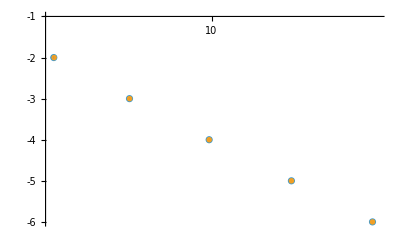

```mathematica
ll=0.015;
Show[plotlistTimeCForAve,plotMarkerListCForTime,plotMiniBarC4ForTime,plotMiniBarC8ForTime,plotMiniBarC16ForTime,plotMiniBarC32ForTime,plotMiniBarC64ForTime,PlotRange->{{8+0.06,12}(*{9,9.1}*),{-6,-1}},AxesOrigin->{8,-1},Ticks->{Table[{1ii,ToString[1ii],ll},{ii,2,20}],Table[{-1ii,ToString[-1ii],ll},{ii,1,6}]},BaseStyle->{14,FontFamily->"Helvetica"}]
```